# q q̄→μ μ in EW theory (SM ): gauge invariance Vertices/Self en.

### PROCESS:

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
Neglect[MM] = Neglect[MM2] = 0;
Neglect[mgamma]=0;
process ={-F[3, {1}], F[3, {1}]} -> {-F[2, {2}], F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SM",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];
SetOptions[CalcFeynAmp,PaVeReduce->True];
SetOptions[CreateFeynAmp, GaugeRules -> {GaugeXi[Z] -> ZGAUGE, GaugeXi[A] -> AGAUGE,
 GaugeXi[W] -> WGAUGE} ];
```

## SM: Feynman rules

Definisco valori di cariche e masse sostituite poi nei passaggi finali

```mathematica
CHARGESZl={QZLl->-1,QZUl->2/3,QZDl->-1/3,I3D->-1/2,I3L->-1/2,I3N->1/2,I3U->1/2}
CHARGESZr={QZLr->-1,QZUr->2/3,QZDr->-1/3}
CHARGESphl={QLl->-1,QUl->2/3,QDl->-1/3}
CHARGESphr={QLr->-1,QUr->2/3,QDr->-1/3}
MASSES={MU->0,MU2->0,MM->0,MM2->0,S+T+U->0}
MGAMMA0={mgamma->0,_mgamma->0};
```

{QZLl→-1,QZUl→2/3,QZDl→-1/3,I3D→-1/2,I3L→-1/2,I3N→1/2,I3U→1/2}

{QZLr→-1,QZUr→2/3,QZDr→-1/3}

{QLl→-1,QUl→2/3,QDl→-1/3}

{QLr→-1,QUr→2/3,QDr→-1/3}

{MU→0,MU2→0,MM→0,MM2→0,S+T+U→0}

```mathematica
(*GENERALIZZAZIONE CARICHE/ISOSPIN PER CASO SM*)
coupling[x_]:=Module[{Mcouplin,chargenuZ,chargelepZ,chargeupZ,chargedownZ,n,m,chargenup,chargelep,chargedown,chargeup},

Mcouplin=M$CouplingMatrices;
(*____________________________  Z COUPLING  ______________________________*)
(*neutrino*)
chargenuZ[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[2]])==rhs_]:=
lhs==(rhs/.{
	dZZZ1-> 2 I3N dZZZ1,
	1/(2 CW SW)->I3N/(CW SW),
	EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
	

});
chargenuZ[other_]=other;
Mcouplin=chargenuZ/@Mcouplin;

(*lepton*)
chargelepZ[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3L*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			SW/CW->-QZLl SW/CW,
			(-1/2+SW^2)->(I3L-QZLl*SW^2),
			dZAZ1->- QLl dZAZ1 (*CT misto gamma Z*)
			},
		rhsR/.{
		SW/CW->-QZLr SW/CW,
		dZAZ1->- QLr dZAZ1 (*CT misto gamma Z*)
		}
});
chargelepZ[other_]=other;
Mcouplin=chargelepZ/@Mcouplin;

(*q up*)
chargeupZ[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3U*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(1/2-2/3SW^2)->(I3U-QZUl*SW^2),
			
			dZAZ1->3/2 QUl dZAZ1,(*CT misto gamma Z: − δ [g1,g2] QU δZ(γZ)/2*)
			-2/3->-QZUl},
		rhsR/.{
			-dZAZ1 /3->-QUr*dZAZ1 /2, (*CT misto gamma Z*)
			-1/3 I*EL->-QZUr/2 I*EL,
			-2/3*I->-QZUr*I,
			-2/3->-QZUr,
			-SW /(3*CW)->-QZUr*SW /(2*CW)}
});
chargeupZ[other_]=other;
Mcouplin=chargeupZ/@Mcouplin;

(*q down*)
chargedownZ[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{
			-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3D*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),
			dZAZ1->-3 QDl dZAZ1, (*CT misto gamma Z*)
			1/3->-QZDl},
			
		rhsR/.{
			dZZZ1->- 3 QZDr*dZZZ1 ,
			dZAZ1->- 3 QDr*dZAZ1 ,(*CT misto gamma Z*)
			1/3 I*EL->-QZDr I*EL,
			1/3*I->-QZDr*I,
			1/3->-QZDr,
			SW /(3*CW)->-QZDr*SW /(CW)}
});
chargedownZ[other_]=other;
Mcouplin=chargedownZ/@Mcouplin;

(*____________________________  GAMMA COUPLING  ___________________________*)
(*neutrino*)
chargenup[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[1]])==rhs_]:=
lhs==(rhs/.{
		EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
});
chargenup[other_]=other;
Mcouplin=chargenup/@Mcouplin;
(*lepton*)
chargelep[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+SW^2)->(I3L-QZLl*SW^2)/-QLl,(*CT misto gamma Z*)
			I->-QLl*I,
			1/2*I->-1/2 QLl*I
},
			
		rhsR/.{dZZA1->- QZLr dZZA1/-QLr,(*CT misto gamma Z*)
		I->-QLr*I,
			1/2*I->-1/2 QLr*I
		}
});
chargelep[other_]=other;
Mcouplin=chargelep/@Mcouplin;

(*q up*)
chargeup[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(1/2-2/3SW^2)->(I3U-QZUl*SW^2),(*CT misto gamma Z*)
			-2/3->-QUl,
			-2/3*I->-QUl*I},
			
		rhsR/.{dZZA1->3/2 QZUr dZZA1,(*CT misto gamma Z*)
		-2/3->-QUr,
		-2/3*I->-QUr*I}
});
chargeup[other_]=other;
Mcouplin=chargeup/@Mcouplin;

(*q down*)
chargedown[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),(*CT misto gamma Z*)
			1/3->-QDl,
			1/3*I->-QDl*I
			},
							
	rhsR/.{ dZZA1->-3 QZDr dZZA1,(*CT misto gamma Z*)
			1/3->-QDr,
			1/3*I->-QDr*I}
});
chargedown[other_]=other;
Mcouplin=chargedown/@Mcouplin;

Mcouplin
];
```

```mathematica
InitializeModel["SM",
ModelEdit :>{
M$ClassesDescription=M$ClassesDescription//.{(-Charge)->QL Charge,(2/3Charge)->QU Charge,(-1/3Charge)->QD Charge(*,
M$ClassesDescription[[5,2,3,2]]->mgamma*)},
M$CouplingMatrices=coupling[M$CouplingMatrices]}

];
```

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

## Feynman Diagrams

## Tree Level

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams



FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-31.frm

running FORM...

ok

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins]//.MGAMMA0;
born = CalcFeynAmp[born1];
```

## Self Energies

```mathematica
tops2 = CreateTopologies[1, 2 -> 2, SelfEnergiesOnly];
ins2 = InsertFields[tops2, process];
ins2 = DiagramSelect[ins2, FreeQ[#, Field[5|6] -> S]&];
Paint[ins2,ColumnsXRows->{11,7},Numbering->Simple,
SheetHeader->None,ImageSize->{1212,756}]
selfff=CreateFeynAmp[ins2];
```

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 65 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

Restoring 18 field point(s)

in total: 75 Particles insertions

> Top. 1 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 2 aebe/cfdf/egfhghgh.m, 0 diagrams

-Graphics-

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5] | [6] | [7] | [8] | [9] | [10] | [11]
[12] | [13] | [14] | [15] | [16] | [17] | [18] | [19] | [20] | [21] | [22]
[23] | [24] | [25] | [26] | [27] | [28] | [29] | [30] | [31] | [32] | [33]
[34] | [35] | [36] | [37] | [38] | [39] | [40] | [41] | [42] | [43] | [44]
[45] | [46] | [47] | [48] | [49] | [50] | [51] | [52] | [53] | [54] | [55]
[56] | [57] | [58] | [59] | [60] | [61] | [62] | [63] | [64] | [65] | [66]
[67] | [68] | [69] | [70] | [71] | [72] | [73] | [74] | [75] | Null | Null)]

creating amplitudes at level(s) {Particles}

> Top. 1: 10 Particles amplitudes

> Top. 2: 65 Particles amplitudes

in total: 75 Particles amplitudes

#### Calcolo feynamp

```mathematica
self=CalcFeynAmp[Take[selfff,{1,20}]//.MGAMMA0][[1]];
self1=CalcFeynAmp[Take[selfff,{21,30}]//.MGAMMA0][[1]];
self2=CalcFeynAmp[Take[selfff,{31,41}]//.MGAMMA0][[1]];
self3=CalcFeynAmp[Take[selfff,{42,47}]//.MGAMMA0][[1]];
self8=CalcFeynAmp[Take[selfff,{48,52}]//.MGAMMA0][[1]];
self4=CalcFeynAmp[Take[selfff,{53,63}]//.MGAMMA0][[1]];
self5=CalcFeynAmp[Take[selfff,{64,70}]//.MGAMMA0][[1]];
```

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-31.frm

running FORM...

ok

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-31.frm

running FORM...

ok

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-31.frm

running FORM...

ok

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-31.frm

running FORM...

ok

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-31.frm

running FORM...

ok

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-31.frm

running FORM...

ok

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-31.frm

running FORM...

ok

```mathematica
self6=CalcFeynAmp[Take[selfff,{71,74}]//.MGAMMA0][[1]];
```

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-31.frm

running FORM...

ok

```mathematica
self7=CalcFeynAmp[Take[selfff,{75}]//.MGAMMA0][[1]];
```

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-31.frm

running FORM...

ok

```mathematica
selftot=self+self1+self2+self3+self4+self5+self6+self7+self8;
```

### UV divergent part Self-energies:

```mathematica
selftot1=Unabbr[selftot];
provvself=Collect[%,WeylChain[__]];
```

```mathematica
selfdiv= UVDivergentPart[selftot];
provaself = Unabbr[SSSSS*selfdiv] ;
```

## Vertices

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 7 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 8 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

Restoring 18 field point(s)

in total: 15 Particles insertions

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

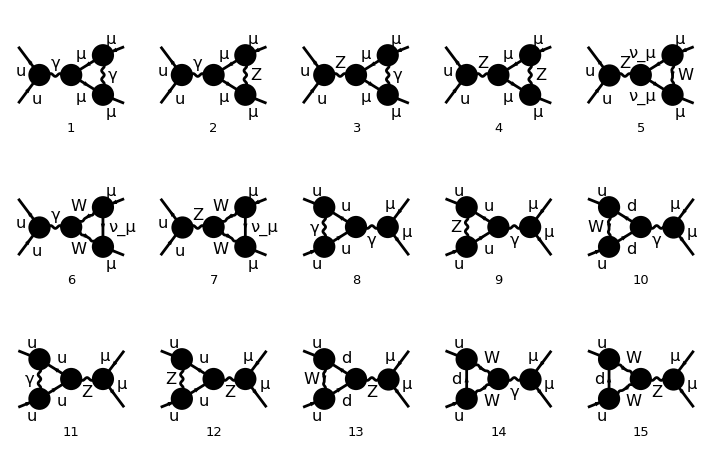

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-31.frm

running FORM...

ok

```mathematica
tops4 = CreateTopologies[1, 2 -> 2, TrianglesOnly];
ins4 = InsertFields[tops4, process];
ins4 = DiagramSelect[ins4, FreeQ[#, Field[5] -> S]&];
Paint[ins4,ColumnsXRows->{5,3},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
verttt=CreateFeynAmp[ins4];
vert = CalcFeynAmp[verttt//.MGAMMA0];
```

```mathematica
verttot=vert[[1]];
```

### UV divergent part Vertices:

```mathematica
verttot1=Unabbr[verttot];
provvert=Collect[%,WeylChain[__]];
```

```mathematica
vertdiv = UVDivergentPart[verttot];
provavert = Unabbr[VVVVV *vertdiv] ;
```

## Boxes

```mathematica
tops5 = CreateTopologies[1, 2 -> 2, BoxesOnly];
ins5 = InsertFields[tops5, process];
(*Paint[ins5,ColumnsXRows->{3,3},Numbering->Simple,
SheetHeader->None,ImageSize->{612,556}]*)
box1=  CreateFeynAmp[ins5];
```

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 4 Particles insertions

> Top. 8: 5 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

Restoring 18 field point(s)

in total: 9 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 9 Particles amplitudes

## Counterterms (CT)

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 4 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

Restoring 18 field point(s)

in total: 8 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebe/cfdf/gegf.m, 0 diagrams

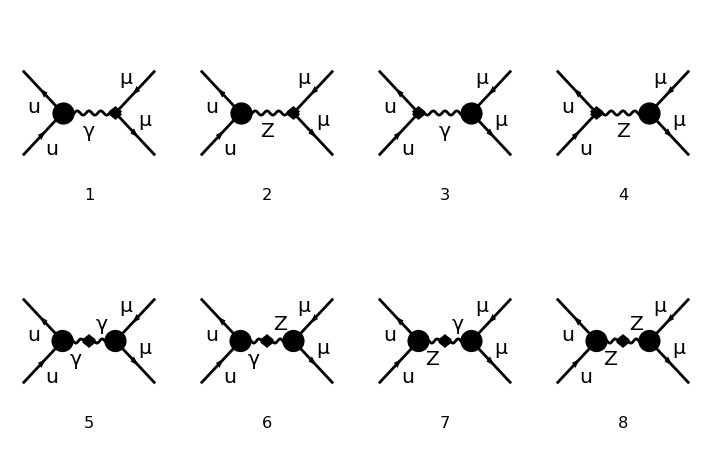

FeynArtsGraphics[][([1] | [2] | [3] | [4]
[5] | [6] | [7] | [8])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 4 Particles amplitudes

in total: 8 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-31.frm

running FORM...

ok

```mathematica
tops1 = CreateCTTopologies[1, 2 -> 2,
  ExcludeTopologies -> {TadpoleCTs,WFCorrectionCTs (*loop counterterms*)}];
ins1 = InsertFields[tops1, process];
Paint[ins1,ColumnsXRows->{4,2},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
counter = CreateFeynAmp[ins1];
ct=CalcFeynAmp[counter];
counterterms = Unabbr[ct];
```

### Renormalization Constants (RC)

```mathematica
rc=CalcRenConst[counterterms];
```

dMWsq1

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 6 Particles insertions

> Top. 2: 17 Particles insertions

Restoring 18 field point(s)

in total: 23 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 6 Particles amplitudes

> Top. 2: 17 Particles amplitudes

in total: 23 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-31.frm

running FORM...

ok

dMZsq1

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 4 Particles insertions

> Top. 2: 20 Particles insertions

Restoring 18 field point(s)

in total: 24 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 20 Particles amplitudes

in total: 24 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-31.frm

running FORM...

ok

dSW1

dZAA1

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 15 Particles insertions

Restoring 18 field point(s)

in total: 17 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 15 Particles amplitudes

in total: 17 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-31.frm

running FORM...

ok

dZAZ1

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 15 Particles insertions

Restoring 18 field point(s)

in total: 17 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 15 Particles amplitudes

in total: 17 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-31.frm

running FORM...

ok

dZe1

dZZA1

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 15 Particles insertions

Restoring 18 field point(s)

in total: 17 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 15 Particles amplitudes

in total: 17 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-31.frm

running FORM...

ok

dZZZ1

dZfL1[2,2,2]

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 3 Particles insertions

Restoring 18 field point(s)

in total: 3 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

in total: 3 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-31.frm

running FORM...

ok

dZfL1[3,1,1]

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 3 Particles insertions

Restoring 18 field point(s)

in total: 3 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

in total: 3 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-31.frm

running FORM...

ok

dZfR1[2,2,2]

dZfR1[3,1,1]

```mathematica
fff=Table[rc[[1,i]]//Simplify,{i,1,Length[rc[[1]]]}];
```

```mathematica
ddd=Table[UVDivergentPart[rc[[1,i]]]//Simplify,{i,1,Length[rc[[1]]]}];
```

```mathematica
fff[[4]]//.IGram'[0]->-IGram[0]^2//.Re[x_]->x//.{Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x)}//FullSimplify;
w2=%//.CW2->1-SW2 //FullSimplify;
Collect[w2,IGram[0],SMFullSimplify];(*ved calcolo quad fff[4],il coefff IGram[0]^2 si annulla*)
```

```mathematica
fff[[4]]=%//.A0[MW2]-A0[MW2 WGAUGE]->-MW2 (-1+WGAUGE) B0i[bb0,0,MW2,MW2 WGAUGE]
```

dZAA1→1/(576 MW2 π)Alfa (-60 A0[MW2]+36 A0[MW2 WGAUGE]+MW2 (8 Finite (-22+36 QDl^2+36 QDr^2+12 QLl^2+12 QLr^2+36 QUl^2+36 QUr^2+25 WGAUGE)+636 B0i[bb0,0,MW2,MW2]-3 (1+59 WGAUGE) B0i[bb0,0,MW2,MW2 WGAUGE]+96 (-(QLl^2+QLr^2) (B0i[bb0,0,ME2,ME2]+B0i[bb0,0,ML2,ML2]+B0i[bb0,0,MM2,MM2])+ME2 (QLl^2-6 QLl QLr+QLr^2) B0i[dbb0,0,ME2,ME2]+ML2 (QLl^2-6 QLl QLr+QLr^2) B0i[dbb0,0,ML2,ML2]+MM2 (QLl^2-6 QLl QLr+QLr^2) B0i[dbb0,0,MM2,MM2])+288 (-(QDl^2+QDr^2) (B0i[bb0,0,MB2,MB2]+B0i[bb0,0,MD2,MD2]+B0i[bb0,0,MS2,MS2])+MB2 (QDl^2-6 QDl QDr+QDr^2) B0i[dbb0,0,MB2,MB2]+MD2 (QDl^2-6 QDl QDr+QDr^2) B0i[dbb0,0,MD2,MD2]+MS2 (QDl^2-6 QDl QDr+QDr^2) B0i[dbb0,0,MS2,MS2])+288 (-(QUl^2+QUr^2) (B0i[bb0,0,MC2,MC2]+B0i[bb0,0,MT2,MT2]+B0i[bb0,0,MU2,MU2])+MC2 (QUl^2-6 QUl QUr+QUr^2) B0i[dbb0,0,MC2,MC2]+MT2 (QUl^2-6 QUl QUr+QUr^2) B0i[dbb0,0,MT2,MT2]+MU2 (QUl^2-6 QUl QUr+QUr^2) B0i[dbb0,0,MU2,MU2])+576 MW2 B0i[dbb0,0,MW2,MW2]+12 MW2 (-1+WGAUGE) (9+11 WGAUGE) B0i[dbb0,0,MW2,MW2 WGAUGE]))+1/(192 π)Alfa (7 (7-19 WGAUGE) A0[MW2]+3 (-15+43 WGAUGE) A0[MW2 WGAUGE]+MW2 (-1+WGAUGE) (2 Finite (1+WGAUGE)+(49-129 WGAUGE) B0i[bb0,0,MW2,MW2 WGAUGE]+4 MW2 (-1+WGAUGE)^2 B0i[dbb0,0,MW2,MW2 WGAUGE])) IGram[0]

i fattori fff[[4]] e  dself senza  //.IGram[x_]→1/x sono uguali a meno di un fattore -1 quindi sostituisco fff[[4]] con - dself

```mathematica
Collect[rc[[1,4,2]]//.IGram'[0]->-IGram[0]^2//.Re[x_]->x//.{Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x)}//.{QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr}//.Finite->1//.{QUl->QU,QLl->QL,QUr->QU,QLr->QL,QDl->QD,
QDr->QD},B0i[__],Simplify];
Select[%,MemberQ[#,WGAUGE,Infinity]&]
Collect[%,IGram[_],Simplify]//.A0[MW2]-A0[MW2 WGAUGE]->-MW2 (-1+WGAUGE) B0i[bb0,0,MW2,MW2 WGAUGE]
```

(Alfa MW2 (1-WGAUGE) B0i[bb0,0,MW2,MW2 WGAUGE] (-1-59 WGAUGE-MW2 (49-178 WGAUGE+129 WGAUGE^2) IGram[0]-8 MW2^2 (-1+WGAUGE)^3 IGram[0]^2))/(192 π (MW2-MW2 WGAUGE))+(Alfa MW2 (-1+WGAUGE) B0i[dbb0,0,MW2,MW2 WGAUGE] (9+MW2 IGram[0]+MW2 WGAUGE^2 IGram[0]+WGAUGE (11-2 MW2 IGram[0])))/(48 π)+1/(576 MW2 π)Alfa (2 MW2 (-88+288 QD^2+96 QL^2+288 QU^2+100 WGAUGE-3 MW2 IGram[0]+3 MW2 WGAUGE^2 IGram[0])-3 A0[MW2] (20+7 MW2 (-7+19 WGAUGE) IGram[0]+8 MW2^2 (-1+WGAUGE)^2 IGram[0]^2)+3 A0[MW2 WGAUGE] (12+3 MW2 (-15+43 WGAUGE) IGram[0]+8 MW2^2 (-1+WGAUGE)^2 IGram[0]^2))

1/(576 MW2 π)Alfa (-60 A0[MW2]+36 A0[MW2 WGAUGE]+MW2 (8 (-22+72 QD^2+24 QL^2+72 QU^2+25 WGAUGE)-3 (1+59 WGAUGE) B0i[bb0,0,MW2,MW2 WGAUGE]+12 MW2 (-9-2 WGAUGE+11 WGAUGE^2) B0i[dbb0,0,MW2,MW2 WGAUGE]))+1/(192 π)Alfa (-7 (-7+19 WGAUGE) A0[MW2]+3 (-15+43 WGAUGE) A0[MW2 WGAUGE]+MW2 (-1+WGAUGE) ((49-129 WGAUGE) B0i[bb0,0,MW2,MW2 WGAUGE]+2 (1+WGAUGE+2 MW2 (-1+WGAUGE)^2 B0i[dbb0,0,MW2,MW2 WGAUGE]))) IGram[0]

```mathematica
Collect[dself//.{QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr}//.Finite->1//.{QUl->QU,QLl->QL,QUr->QU,QLr->QL,QDl->QD,
QDr->QD},B0i[__],Simplify]
Select[%,MemberQ[#,WGAUGE,Infinity]&]
```

-(Alfa (4 MW2 (-1+6 QD^2+2 QL^2+6 QU^2+WGAUGE)+(9+WGAUGE) A0[MW2]-(9+WGAUGE) A0[MW2 WGAUGE]))/(24 MW2 π)+(Alfa QD^2 B0i[bb0,0,MB2,MB2])/π+(Alfa QU^2 B0i[bb0,0,MC2,MC2])/π+(Alfa QD^2 B0i[bb0,0,MD2,MD2])/π+(Alfa QL^2 B0i[bb0,0,ME2,ME2])/(3 π)+(Alfa QL^2 B0i[bb0,0,ML2,ML2])/(3 π)+(Alfa QL^2 B0i[bb0,0,MM2,MM2])/(3 π)+(Alfa QD^2 B0i[bb0,0,MS2,MS2])/π+(Alfa QU^2 B0i[bb0,0,MT2,MT2])/π+(Alfa QU^2 B0i[bb0,0,MU2,MU2])/π-(17 Alfa B0i[bb0,0,MW2,MW2])/(12 π)-(Alfa (-19+2 WGAUGE+WGAUGE^2) B0i[bb0,0,MW2,MW2 WGAUGE])/(24 π)+(2 Alfa MB2 QD^2 B0i[dbb0,0,MB2,MB2])/π+(2 Alfa MC2 QU^2 B0i[dbb0,0,MC2,MC2])/π+(2 Alfa MD2 QD^2 B0i[dbb0,0,MD2,MD2])/π+(2 Alfa ME2 QL^2 B0i[dbb0,0,ME2,ME2])/(3 π)+(2 Alfa ML2 QL^2 B0i[dbb0,0,ML2,ML2])/(3 π)+(2 Alfa MM2 QL^2 B0i[dbb0,0,MM2,MM2])/(3 π)+(2 Alfa MS2 QD^2 B0i[dbb0,0,MS2,MS2])/π+(2 Alfa MT2 QU^2 B0i[dbb0,0,MT2,MT2])/π+(2 Alfa MU2 QU^2 B0i[dbb0,0,MU2,MU2])/π-(Alfa MW2 B0i[dbb0,0,MW2,MW2])/π+(Alfa MW2 (-1+WGAUGE)^2 B0i[dbb0,0,MW2,MW2 WGAUGE])/(12 π)

-(Alfa (4 MW2 (-1+6 QD^2+2 QL^2+6 QU^2+WGAUGE)+(9+WGAUGE) A0[MW2]-(9+WGAUGE) A0[MW2 WGAUGE]))/(24 MW2 π)-(Alfa (-19+2 WGAUGE+WGAUGE^2) B0i[bb0,0,MW2,MW2 WGAUGE])/(24 π)+(Alfa MW2 (-1+WGAUGE)^2 B0i[dbb0,0,MW2,MW2 WGAUGE])/(12 π)

```mathematica
dselfr=DSelfEnergy[V[1]->V[1],q]//.IGram'[x_]->-IGram[x]^2//.IGram[x_]->1/x//.{Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x)}//SMFullSimplify;
dself=%//.q->0 //FullSimplify;
fff[[4]][[2]]=-dself;
fff[[4]]
```

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 15 Particles insertions

Restoring 18 field point(s)

in total: 17 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 15 Particles amplitudes

in total: 17 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-31.frm

running FORM...

ok

dZAA1→-1/(24 MW2 π)Alfa (-(9+WGAUGE) A0[MW2]+(9+WGAUGE) A0[MW2 WGAUGE]+MW2 (4 (-Finite (-1+3 QDl^2+3 QDr^2+QLl^2+QLr^2+3 QUl^2+3 QUr^2+WGAUGE)+(QLl^2+QLr^2) (B0i[bb0,0,ME2,ME2]+B0i[bb0,0,ML2,ML2]+B0i[bb0,0,MM2,MM2])+3 (QDl^2+QDr^2) (B0i[bb0,0,MB2,MB2]+B0i[bb0,0,MD2,MD2]+B0i[bb0,0,MS2,MS2])+3 (QUl^2+QUr^2) (B0i[bb0,0,MC2,MC2]+B0i[bb0,0,MT2,MT2]+B0i[bb0,0,MU2,MU2]))-34 B0i[bb0,0,MW2,MW2]+19 B0i[bb0,0,MW2,MW2 WGAUGE])+MW2 (-WGAUGE (2+WGAUGE) B0i[bb0,0,MW2,MW2 WGAUGE]-12 (QDl^2-6 QDl QDr+QDr^2) (MB2 B0i[dbb0,0,MB2,MB2]+MD2 B0i[dbb0,0,MD2,MD2]+MS2 B0i[dbb0,0,MS2,MS2])-4 ((QLl^2-6 QLl QLr+QLr^2) (ME2 B0i[dbb0,0,ME2,ME2]+ML2 B0i[dbb0,0,ML2,ML2]+MM2 B0i[dbb0,0,MM2,MM2])+3 (QUl^2-6 QUl QUr+QUr^2) (MC2 B0i[dbb0,0,MC2,MC2]+MT2 B0i[dbb0,0,MT2,MT2]+MU2 B0i[dbb0,0,MU2,MU2])+6 MW2 B0i[dbb0,0,MW2,MW2])+2 MW2 (-1+WGAUGE)^2 B0i[dbb0,0,MW2,MW2 WGAUGE]))

```mathematica
Collect[fff[[4,2]],{B0i[bb0,0,MW2,MW2 WGAUGE],B0i[dbb0,0,MW2,MW2 WGAUGE],A0[MW2 WGAUGE],A0[MW2]},Simplify]
fff[[4,2]]=%//.{A0[MW2 WGAUGE]->0,A0[MW2]->(1-WGAUGE)MW2 B0i[bb0,0,MW2,MW2 WGAUGE]}//Simplify;
Collect[%,{B0i[bb0,0,MW2,MW2 WGAUGE],B0i[dbb0,0,MW2,MW2 WGAUGE]},Simplify]
```

(Alfa (9+WGAUGE) A0[MW2])/(24 MW2 π)-(Alfa (9+WGAUGE) A0[MW2 WGAUGE])/(24 MW2 π)+(Alfa (-19+2 WGAUGE+WGAUGE^2) B0i[bb0,0,MW2,MW2 WGAUGE])/(24 π)-1/(12 π)Alfa (-2 Finite (-1+3 QDl^2+3 QDr^2+QLl^2+QLr^2+3 QUl^2+3 QUr^2+WGAUGE)+2 (QLl^2+QLr^2) (B0i[bb0,0,ME2,ME2]+B0i[bb0,0,ML2,ML2]+B0i[bb0,0,MM2,MM2])+6 (QDl^2+QDr^2) (B0i[bb0,0,MB2,MB2]+B0i[bb0,0,MD2,MD2]+B0i[bb0,0,MS2,MS2])+6 (QUl^2+QUr^2) (B0i[bb0,0,MC2,MC2]+B0i[bb0,0,MT2,MT2]+B0i[bb0,0,MU2,MU2])-17 B0i[bb0,0,MW2,MW2]-2 (QLl^2-6 QLl QLr+QLr^2) (ME2 B0i[dbb0,0,ME2,ME2]+ML2 B0i[dbb0,0,ML2,ML2]+MM2 B0i[dbb0,0,MM2,MM2])-6 (QDl^2-6 QDl QDr+QDr^2) (MB2 B0i[dbb0,0,MB2,MB2]+MD2 B0i[dbb0,0,MD2,MD2]+MS2 B0i[dbb0,0,MS2,MS2])-6 (QUl^2-6 QUl QUr+QUr^2) (MC2 B0i[dbb0,0,MC2,MC2]+MT2 B0i[dbb0,0,MT2,MT2]+MU2 B0i[dbb0,0,MU2,MU2])-12 MW2 B0i[dbb0,0,MW2,MW2])-(Alfa MW2 (-1+WGAUGE)^2 B0i[dbb0,0,MW2,MW2 WGAUGE])/(12 π)

-(Alfa (5+3 WGAUGE) B0i[bb0,0,MW2,MW2 WGAUGE])/(12 π)+1/(12 π)Alfa (2 Finite (-1+3 QDl^2+3 QDr^2+QLl^2+QLr^2+3 QUl^2+3 QUr^2+WGAUGE)-2 (QLl^2+QLr^2) (B0i[bb0,0,ME2,ME2]+B0i[bb0,0,ML2,ML2]+B0i[bb0,0,MM2,MM2])-6 (QDl^2+QDr^2) (B0i[bb0,0,MB2,MB2]+B0i[bb0,0,MD2,MD2]+B0i[bb0,0,MS2,MS2])-6 (QUl^2+QUr^2) (B0i[bb0,0,MC2,MC2]+B0i[bb0,0,MT2,MT2]+B0i[bb0,0,MU2,MU2])+17 B0i[bb0,0,MW2,MW2]+2 (QLl^2-6 QLl QLr+QLr^2) (ME2 B0i[dbb0,0,ME2,ME2]+ML2 B0i[dbb0,0,ML2,ML2]+MM2 B0i[dbb0,0,MM2,MM2])+6 (QDl^2-6 QDl QDr+QDr^2) (MB2 B0i[dbb0,0,MB2,MB2]+MD2 B0i[dbb0,0,MD2,MD2]+MS2 B0i[dbb0,0,MS2,MS2])+6 (QUl^2-6 QUl QUr+QUr^2) (MC2 B0i[dbb0,0,MC2,MC2]+MT2 B0i[dbb0,0,MT2,MT2]+MU2 B0i[dbb0,0,MU2,MU2])+12 MW2 B0i[dbb0,0,MW2,MW2])-(Alfa MW2 (-1+WGAUGE)^2 B0i[dbb0,0,MW2,MW2 WGAUGE])/(12 π)

```mathematica
fff[[7]]//.IGram'[0]->-IGram[0]^2//.Re[x_]->x//.{Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x)}//FullSimplify;
w1=%//.CW2->1-SW2 //FullSimplify;
Collect[w1,IGram[0],SMFullSimplify](*ved calcolo quad fff[7],il coefff si annulla!*)
fff[[7]]=%//.A0[MW2]-A0[MW2 WGAUGE]->-MW2 (-1+WGAUGE) B0i[bb0,0,MW2,MW2 WGAUGE]
```

dZZA1→1/(48 CW MZ2^2 π SW)Alfa (MW2 (1-WGAUGE) (-8 Finite MZ2-3 MW2 (1+WGAUGE)+4 Finite MW2 (3+WGAUGE))+6 MW2 (-13+4 WGAUGE) A0[MW2]-4 MW2 A0[MW2 WGAUGE]+16 (-MW2+MZ2) A0[MW2 WGAUGE]-22 MW2 WGAUGE A0[MW2 WGAUGE]+8 (Finite (-4 (3 I3D (MB2+MD2+MS2) MZ2 QDl+I3L (ME2+ML2+MM2) MZ2 QLl-3 (MB2+MD2+MS2) MZ2 (QDl QZDl+QDr QZDr) SW2-(ME2+ML2+MM2) MZ2 (QLl QZLl+QLr QZLr) SW2+3 (MC2+MT2+MU2) (I3U MZ2 QUl-MZ2 (QUl QZUl+QUr QZUr) SW2))-2 MW2 MZ2 WGAUGE+MW2^2 (11+WGAUGE))+4 (I3L MZ2 QLl-MZ2 (QLl QZLl+QLr QZLr) SW2) (A0[ME2]+A0[ML2]+A0[MM2])+12 (I3D MZ2 QDl-MZ2 (QDl QZDl+QDr QZDr) SW2) (A0[MB2]+A0[MD2]+A0[MS2])+12 (I3U MZ2 QUl-MZ2 (QUl QZUl+QUr QZUr) SW2) (A0[MC2]+A0[MT2]+A0[MU2])+2 (I3L MZ2 (QLl-3 QLr)-MZ2 (QLl (QZLl-3 QZLr)+QLr (-3 QZLl+QZLr)) SW2) (ME2 B0i[bb0,0,ME2,ME2]+ML2 B0i[bb0,0,ML2,ML2]+MM2 B0i[bb0,0,MM2,MM2])+6 (MB2 (I3D MZ2 (QDl-3 QDr)-MZ2 (QDl (QZDl-3 QZDr)+QDr (-3 QZDl+QZDr)) SW2) B0i[bb0,0,MB2,MB2]+MC2 (I3U MZ2 (QUl-3 QUr)-MZ2 (QUl (QZUl-3 QZUr)+QUr (-3 QZUl+QZUr)) SW2) B0i[bb0,0,MC2,MC2]+MD2 (I3D MZ2 (QDl-3 QDr)-MZ2 (QDl (QZDl-3 QZDr)+QDr (-3 QZDl+QZDr)) SW2) B0i[bb0,0,MD2,MD2]+MS2 (I3D MZ2 (QDl-3 QDr)-MZ2 (QDl (QZDl-3 QZDr)+QDr (-3 QZDl+QZDr)) SW2) B0i[bb0,0,MS2,MS2]+MT2 (I3U MZ2 (QUl-3 QUr)-MZ2 (QUl (QZUl-3 QZUr)+QUr (-3 QZUl+QZUr)) SW2) B0i[bb0,0,MT2,MT2]+MU2 (I3U MZ2 (QUl-3 QUr)-MZ2 (QUl (QZUl-3 QZUr)+QUr (-3 QZUl+QZUr)) SW2) B0i[bb0,0,MU2,MU2]))+96 MW2^2 B0i[bb0,0,MW2,MW2]+18 MW2^2 B0i[bb0,0,MW2,MW2 WGAUGE]+36 MW2 (-MW2+MZ2) B0i[bb0,0,MW2,MW2 WGAUGE]-8 MW2^2 WGAUGE B0i[bb0,0,MW2,MW2 WGAUGE]-4 MW2 MZ2 SW2 WGAUGE B0i[bb0,0,MW2,MW2 WGAUGE]+22 MW2^2 WGAUGE^2 B0i[bb0,0,MW2,MW2 WGAUGE])+(Alfa MW2 (2 MZ2+MW2 (-1+WGAUGE)) (-1+WGAUGE) (A0[MW2]-A0[MW2 WGAUGE]+MW2 (-1+WGAUGE) B0i[bb0,0,MW2,MW2 WGAUGE]) IGram[0])/(24 CW MZ2^2 π SW)

dZZA1→1/(48 CW MZ2^2 π SW)Alfa (MW2 (1-WGAUGE) (-8 Finite MZ2-3 MW2 (1+WGAUGE)+4 Finite MW2 (3+WGAUGE))+6 MW2 (-13+4 WGAUGE) A0[MW2]-4 MW2 A0[MW2 WGAUGE]+16 (-MW2+MZ2) A0[MW2 WGAUGE]-22 MW2 WGAUGE A0[MW2 WGAUGE]+8 (Finite (-4 (3 I3D (MB2+MD2+MS2) MZ2 QDl+I3L (ME2+ML2+MM2) MZ2 QLl-3 (MB2+MD2+MS2) MZ2 (QDl QZDl+QDr QZDr) SW2-(ME2+ML2+MM2) MZ2 (QLl QZLl+QLr QZLr) SW2+3 (MC2+MT2+MU2) (I3U MZ2 QUl-MZ2 (QUl QZUl+QUr QZUr) SW2))-2 MW2 MZ2 WGAUGE+MW2^2 (11+WGAUGE))+4 (I3L MZ2 QLl-MZ2 (QLl QZLl+QLr QZLr) SW2) (A0[ME2]+A0[ML2]+A0[MM2])+12 (I3D MZ2 QDl-MZ2 (QDl QZDl+QDr QZDr) SW2) (A0[MB2]+A0[MD2]+A0[MS2])+12 (I3U MZ2 QUl-MZ2 (QUl QZUl+QUr QZUr) SW2) (A0[MC2]+A0[MT2]+A0[MU2])+2 (I3L MZ2 (QLl-3 QLr)-MZ2 (QLl (QZLl-3 QZLr)+QLr (-3 QZLl+QZLr)) SW2) (ME2 B0i[bb0,0,ME2,ME2]+ML2 B0i[bb0,0,ML2,ML2]+MM2 B0i[bb0,0,MM2,MM2])+6 (MB2 (I3D MZ2 (QDl-3 QDr)-MZ2 (QDl (QZDl-3 QZDr)+QDr (-3 QZDl+QZDr)) SW2) B0i[bb0,0,MB2,MB2]+MC2 (I3U MZ2 (QUl-3 QUr)-MZ2 (QUl (QZUl-3 QZUr)+QUr (-3 QZUl+QZUr)) SW2) B0i[bb0,0,MC2,MC2]+MD2 (I3D MZ2 (QDl-3 QDr)-MZ2 (QDl (QZDl-3 QZDr)+QDr (-3 QZDl+QZDr)) SW2) B0i[bb0,0,MD2,MD2]+MS2 (I3D MZ2 (QDl-3 QDr)-MZ2 (QDl (QZDl-3 QZDr)+QDr (-3 QZDl+QZDr)) SW2) B0i[bb0,0,MS2,MS2]+MT2 (I3U MZ2 (QUl-3 QUr)-MZ2 (QUl (QZUl-3 QZUr)+QUr (-3 QZUl+QZUr)) SW2) B0i[bb0,0,MT2,MT2]+MU2 (I3U MZ2 (QUl-3 QUr)-MZ2 (QUl (QZUl-3 QZUr)+QUr (-3 QZUl+QZUr)) SW2) B0i[bb0,0,MU2,MU2]))+96 MW2^2 B0i[bb0,0,MW2,MW2]+18 MW2^2 B0i[bb0,0,MW2,MW2 WGAUGE]+36 MW2 (-MW2+MZ2) B0i[bb0,0,MW2,MW2 WGAUGE]-8 MW2^2 WGAUGE B0i[bb0,0,MW2,MW2 WGAUGE]-4 MW2 MZ2 SW2 WGAUGE B0i[bb0,0,MW2,MW2 WGAUGE]+22 MW2^2 WGAUGE^2 B0i[bb0,0,MW2,MW2 WGAUGE])

Presenza di Pair[nul,nul]:

```mathematica
fff=fff//.{QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr}//.{QUl->QU,QLl->QL,QUr->QU,QLr->QL,QDl->QD,QDr->QD};
```

```mathematica
ggg=fff//.IGram'[x_]->-IGram[x]^2//.IGram[x_]->1/x//.Re[x_]->x//.{Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x)}//Simplify;
```

```mathematica
ggg[[1]]=ggg[[1]]//SMFullSimplify
```

dMWsq1→-1/(288 MW2 MZ2 π SW2)Alfa (Finite MW2^2 (-1+ZGAUGE) (-52 MW2+3 MZ2 (1+ZGAUGE))+3 MW2 (-1+ZGAUGE) (4 Finite (5 MW2^2-MZ2^2-MW2 MZ2 (-2+ZGAUGE))+3 MW2 MZ2 (1+ZGAUGE))-4 Finite MW2 (2 MW2^2 (-10+9 AGAUGE+ZGAUGE)+MW2 MZ2 (-71-18 AGAUGE+9 ZGAUGE)+3 MZ2 (6 MB2+6 MC2+6 MD2+2 ME2-MH2+2 (ML2+MM2+3 (MS2+MT2+MU2))-MZ2 ZGAUGE))+36 (-MB2+MT2+2 MW2) MZ2 A0[MB2]+36 (-MC2+MS2+2 MW2) MZ2 A0[MC2]+36 (-MD2+MU2+2 MW2) MZ2 A0[MD2]-12 (ME2-2 MW2) MZ2 A0[ME2]+6 (MH2-3 MW2) MZ2 A0[MH2]-12 (ML2-2 MW2) MZ2 A0[ML2]-12 (MM2-2 MW2) MZ2 A0[MM2]+36 (MC2-MS2+2 MW2) MZ2 A0[MS2]+36 (MB2-MT2+2 MW2) MZ2 A0[MT2]+36 (MD2-MU2+2 MW2) MZ2 A0[MU2]+6 (-24 MW2^2+8 MW2 MZ2+MZ2^2) A0[MZ2]-36 MW2 MZ2 A0[MW2 WGAUGE]-18 MW2 MZ2 A0[MZ2 ZGAUGE]+12 (ME2-MW2) (ME2+2 MW2) MZ2 B0i[bb0,MW2,0,ME2]+12 (ML2-MW2) (ML2+2 MW2) MZ2 B0i[bb0,MW2,0,ML2]+12 (MM2-MW2) (MM2+2 MW2) MZ2 B0i[bb0,MW2,0,MM2]+36 ((MB2-MT2)^2+(MB2+MT2) MW2-2 MW2^2) MZ2 B0i[bb0,MW2,MB2,MT2]+36 ((MC2-MS2)^2+(MC2+MS2) MW2-2 MW2^2) MZ2 B0i[bb0,MW2,MC2,MS2]+36 ((MD2-MU2)^2+(MD2+MU2) MW2-2 MW2^2) MZ2 B0i[bb0,MW2,MD2,MU2]-6 (MH2^2-4 MH2 MW2+12 MW2^2) MZ2 B0i[bb0,MW2,MH2,MW2]+6 (4 MW2-MZ2) (12 MW2^2+20 MW2 MZ2+MZ2^2) B0i[bb0,MW2,MW2,MZ2]-(72 (-1+AGAUGE) Finite MW2^3 MZ2 SW2 Pair[nul,nul])/(MW2 Pair[nul,nul]-Pair[k[1],nul]^2)+(72 MW2^2 MZ2 SW2 B0i[bb0,MW2,0,MW2] (4 MW2 Pair[nul,nul]-(3+AGAUGE) Pair[k[1],nul]^2))/(MW2 Pair[nul,nul]-Pair[k[1],nul]^2)+(6 A0[MW2] (-MW2 MZ2 (MH2+12 MW2+MZ2) Pair[nul,nul]+(-12 (-1+AGAUGE) MW2^2+12 AGAUGE MW2 MZ2+MZ2 (MH2+MZ2)) Pair[k[1],nul]^2))/(MW2 Pair[nul,nul]-Pair[k[1],nul]^2))

```mathematica
ggg=ggg//.AGAUGE->1//Simplify;
```

## GAUGE INDEPENDENCE

VERTICI:

```mathematica
ctvv=ExpandSums[counterterms[[1]]//.  {dMZsq1->0,dMWsq1->0,dSW1->0,dZAA1->0,dZAZ1->0, dZZZ1->0, dZZA1->0, dZe1->0}//.ggg];
ctvert1=Collect[ ctvv, WeylChain[__]];
```

```mathematica
sommactv=Collect[provvert+ctvert1//.IGram'[x_]->-IGram[x]^2//.{IGram[x_]->1/x,
Conjugate[x_]->x ,Re[x_]->x}(*//.MASSES*)//.{QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr}//.{QUl->QU,QLl->QL,QUr->QU,QLr->QL,QDl->QD,
QDr->QD}//. {Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x) },WeylChain[__]];
```

SELF :

```mathematica
ctss=ExpandSums[counterterms[[1]]//. {dZfL1[__]->0,Conjugate[dZfL1[__]]->0,dZfR1[__]->0,Conjugate[dZfR1[__]]->0}//.ggg];
ctself1=Collect[ ctss, WeylChain[__]];
```

```mathematica
sommacts=Collect[provvself+ctself1//.IGram'[x_]->-IGram[x]^2//.{IGram[x_]->1/x,
Conjugate[x_]->x ,Re[x_]->x}(*//.MASSES*)//.{QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr}//.{QUl->QU,QLl->QL,QUr->QU,QLr->QL,QDl->QD,
QDr->QD}//. {Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x) },WeylChain[__]];
```

VERTICI + SELF :

```mathematica
cttot=ExpandSums[counterterms[[1]]//.ggg];
cttot1=Collect[ cttot, WeylChain[__]];
```

```mathematica
sommatot=Collect[provvert+provvself+cttot1//.IGram'[x_]->-IGram[x]^2//.{IGram[x_]->1/x,
Conjugate[x_]->x ,Re[x_]->x}(*//.MASSES*)//.{QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr}//.{QUl->QU,QLl->QL,QUr->QU,QLr->QL,QDl->QD,
QDr->QD}//. {Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x) },WeylChain[__]];
```

## Z GAUGE

### ZGAUGE VERTICI

In questo caso dovrei ritrovare id Ward, quindi integrali nei ct che si cancellano con integrali dei vertici:
Integrali nel caso massless sono solo 2:
-A0 - è presente solo nei ct
-B0i solo nei vertici
-Non sono presenti integrali C0i[__,MZ2* ZGAUGE]
Risultato: ZGAUGE indipendente

```mathematica
(*A0[MZ2* ZGAUGE]*)
```

```mathematica
listaAv=Union[Cases[sommactv,A0[MZ2* ZGAUGE],Infinity]]
Table[av[i]=listaAv[[i]],{i,1,Length[listaAv]}];
```

{A0[MZ2 ZGAUGE]}

```mathematica
Collect[Table[Coefficient[sommactv,av[i]] ,{i,1,Length[listaAv]}],WeylChain[__],FullSimplify];
Table[{listaAv[[i]]}=={%[[i]]} , {i, 1, Length[listaAv]}]//.MASSES
```

{{A0[MZ2 ZGAUGE]}=={(Alfa2 QL QU (CW2 (MZ2-S)-S SW2) (I3L^2+I3U^2-2 (I3L QL+I3U QU) SW2+2 (QL^2+QU^2) SW2^2) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|u̇ 4)) ((u2|6|v3)))/(CW2^2 MZ2 (MZ2-S) S SW2)+(Alfa2 (I3L^2+I3U^2-2 (I3L QL+I3U QU) SW2+2 (QL^2+QU^2) SW2^2) (QL (CW2 MZ2 QU+(I3U-QU) S) SW2+I3L S (-I3U+QU SW2)) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(CW2^2 MZ2 (MZ2-S) S SW2^2)+(Alfa2 QU (I3L^2+I3U^2-2 (I3L QL+I3U QU) SW2+2 (QL^2+QU^2) SW2^2) (CW2 QL (MZ2-S)+S (I3L-QL SW2)) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(CW2^2 MZ2 (MZ2-S) S SW2)+(Alfa2 QL (I3L^2+I3U^2-2 (I3L QL+I3U QU) SW2+2 (QL^2+QU^2) SW2^2) (CW2 QU (MZ2-S)+S (I3U-QU SW2)) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(CW2^2 MZ2 (MZ2-S) S SW2)}}

```mathematica
(*B0i[__,MZ2* ZGAUGE]*)
```

```mathematica
listaBv=Union[Cases[sommactv,B0i[__,MZ2* ZGAUGE],Infinity]]
Table[bv[i]=listaBv[[i]],{i,1,Length[listaBv]}];
```

{B0i[bb0,MM2,MM2,MZ2 ZGAUGE],B0i[bb0,MU2,MU2,MZ2 ZGAUGE],B0i[dbb0,MM2,MM2,MZ2 ZGAUGE],B0i[dbb0,MU2,MU2,MZ2 ZGAUGE]}

```mathematica
Collect[Table[Coefficient[sommactv,bv[i]] ,{i,1,Length[listaBv]}],WeylChain[__],FullSimplify];
Table[{listaBv[[i]]}=={%[[i]]} , {i, 1, Length[listaBv]}]//.MASSES
```

{{B0i[bb0,0,0,MZ2 ZGAUGE]}=={-(Alfa2 QL QU (CW2 (MZ2-S)-S SW2) (I3L^2 MZ2 ZGAUGE+2 MZ2 QL SW2 (-I3L+QL SW2) ZGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|u̇ 4)) ((u2|6|v3)))/(CW2^2 MZ2 (MZ2-S) S SW2)+(Alfa2 (I3L I3U S-(CW2 MZ2 QL QU+I3U QL S+(I3L-QL) QU S) SW2) (I3L^2-2 I3L QL SW2+2 QL^2 SW2^2) ZGAUGE Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(CW2^2 (MZ2-S) S SW2^2)-(Alfa2 QU (I3L^2-2 I3L QL SW2+2 QL^2 SW2^2) (CW2 QL (MZ2-S)+S (I3L-QL SW2)) ZGAUGE Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(CW2^2 (MZ2-S) S SW2)-(Alfa2 QL (CW2 QU (MZ2-S)+S (I3U-QU SW2)) (I3L^2 MZ2 ZGAUGE+2 MZ2 QL SW2 (-I3L+QL SW2) ZGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(CW2^2 MZ2 (MZ2-S) S SW2)},{B0i[bb0,0,0,MZ2 ZGAUGE]}=={-(Alfa2 QL QU (CW2 (MZ2-S)-S SW2) (I3U^2 MZ2 ZGAUGE+2 MZ2 QU SW2 (-I3U+QU SW2) ZGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|u̇ 4)) ((u2|6|v3)))/(CW2^2 MZ2 (MZ2-S) S SW2)+(Alfa2 (I3L I3U S-(CW2 MZ2 QL QU+I3U QL S+(I3L-QL) QU S) SW2) (I3U^2-2 I3U QU SW2+2 QU^2 SW2^2) ZGAUGE Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(CW2^2 (MZ2-S) S SW2^2)-(Alfa2 QU (CW2 QL (MZ2-S)+S (I3L-QL SW2)) (I3U^2 MZ2 ZGAUGE+2 MZ2 QU SW2 (-I3U+QU SW2) ZGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(CW2^2 MZ2 (MZ2-S) S SW2)-(Alfa2 QL (I3U^2-2 I3U QU SW2+2 QU^2 SW2^2) (CW2 QU (MZ2-S)+S (I3U-QU SW2)) ZGAUGE Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(CW2^2 (MZ2-S) S SW2)},{B0i[dbb0,0,0,MZ2 ZGAUGE]}=={0},{B0i[dbb0,0,0,MZ2 ZGAUGE]}=={0}}

```mathematica
(*B0i[q^2,0,Xi mz2] con q^2=0 si semplifica in (A0[Xi mz2]-A0[0])/Xi mz2*)
sommactv//.A0[MZ2 ZGAUGE]->MZ2 ZGAUGE B0i[bb0,0,0,MZ2 ZGAUGE]; 
a0gauge=Collect[Coefficient[%,B0i[bb0,0,0,MZ2 ZGAUGE]],WeylChain[__],FullSimplify]

Collect[Table[Coefficient[sommactv,bv[i]] ,{i,1,Length[listaBv]}],WeylChain[__],FullSimplify];
zvlistmassless=Table[{listaBv[[i]]}=={%[[i]]} , {i, 1, Length[listaBv]}]//.MASSES
```

(Alfa2 QL QU (CW2 (-MZ2+S)+S SW2) (I3L^2+I3U^2-2 (I3L QL+I3U QU) SW2+2 (QL^2+QU^2) SW2^2) ZGAUGE Mat[SUNT[Col1,Col2]] ((v̇ 1|7|u̇ 4)) ((u2|6|v3)))/(CW2^2 S (-MZ2+S) SW2)+1/(CW2^2 S (-MZ2+S) SW2^2)Alfa2 (I3L I3U S-(CW2 MZ2 QL QU+I3U QL S+(I3L-QL) QU S) SW2) (I3L^2+I3U^2-2 (I3L QL+I3U QU) SW2+2 (QL^2+QU^2) SW2^2) ZGAUGE Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+(Alfa2 QU (-I3L S+CW2 QL (-MZ2+S)+QL S SW2) (I3L^2+I3U^2-2 (I3L QL+I3U QU) SW2+2 (QL^2+QU^2) SW2^2) ZGAUGE Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(CW2^2 S (-MZ2+S) SW2)+(Alfa2 QL (-I3U S+CW2 QU (-MZ2+S)+QU S SW2) (I3L^2+I3U^2-2 (I3L QL+I3U QU) SW2+2 (QL^2+QU^2) SW2^2) ZGAUGE Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(CW2^2 S (-MZ2+S) SW2)

{{B0i[bb0,0,0,MZ2 ZGAUGE]}=={-(Alfa2 QL QU (CW2 (MZ2-S)-S SW2) (I3L^2 MZ2 ZGAUGE+2 MZ2 QL SW2 (-I3L+QL SW2) ZGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|u̇ 4)) ((u2|6|v3)))/(CW2^2 MZ2 (MZ2-S) S SW2)+(Alfa2 (I3L I3U S-(CW2 MZ2 QL QU+I3U QL S+(I3L-QL) QU S) SW2) (I3L^2-2 I3L QL SW2+2 QL^2 SW2^2) ZGAUGE Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(CW2^2 (MZ2-S) S SW2^2)-(Alfa2 QU (I3L^2-2 I3L QL SW2+2 QL^2 SW2^2) (CW2 QL (MZ2-S)+S (I3L-QL SW2)) ZGAUGE Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(CW2^2 (MZ2-S) S SW2)-(Alfa2 QL (CW2 QU (MZ2-S)+S (I3U-QU SW2)) (I3L^2 MZ2 ZGAUGE+2 MZ2 QL SW2 (-I3L+QL SW2) ZGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(CW2^2 MZ2 (MZ2-S) S SW2)},{B0i[bb0,0,0,MZ2 ZGAUGE]}=={-(Alfa2 QL QU (CW2 (MZ2-S)-S SW2) (I3U^2 MZ2 ZGAUGE+2 MZ2 QU SW2 (-I3U+QU SW2) ZGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|u̇ 4)) ((u2|6|v3)))/(CW2^2 MZ2 (MZ2-S) S SW2)+(Alfa2 (I3L I3U S-(CW2 MZ2 QL QU+I3U QL S+(I3L-QL) QU S) SW2) (I3U^2-2 I3U QU SW2+2 QU^2 SW2^2) ZGAUGE Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(CW2^2 (MZ2-S) S SW2^2)-(Alfa2 QU (CW2 QL (MZ2-S)+S (I3L-QL SW2)) (I3U^2 MZ2 ZGAUGE+2 MZ2 QU SW2 (-I3U+QU SW2) ZGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(CW2^2 MZ2 (MZ2-S) S SW2)-(Alfa2 QL (I3U^2-2 I3U QU SW2+2 QU^2 SW2^2) (CW2 QU (MZ2-S)+S (I3U-QU SW2)) ZGAUGE Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(CW2^2 (MZ2-S) S SW2)},{B0i[dbb0,0,0,MZ2 ZGAUGE]}=={0},{B0i[dbb0,0,0,MZ2 ZGAUGE]}=={0}}

```mathematica
zvlistmassless[[1,2,1]]+zvlistmassless[[2,2,1]]+a0gauge//Simplify
```

0

### ZGAUGE SELF

Per le self energie ho 6 tipologie di integrali scalari:
-A0 - è presente sia nei ct che self e nel calcolo sottostante si vede come avviene la cancellazione dei coefficienti
-B0i sono diversi per self e ct, i coefficienti sono tutti nulli
- Non sono presenti integrali C0i[__,MZ2* ZGAUGE]
Risultato: ZGAUGE indipendente (BOX non necessario per gauge invarianza )

```mathematica
(*A0[MZ2* ZGAUGE]*)
```

```mathematica
listaAs=Union[Cases[sommacts,A0[MZ2* ZGAUGE],Infinity]]
Table[as[i]=listaAs[[i]],{i,1,Length[listaAs]}];
```

{A0[MZ2 ZGAUGE]}

```mathematica
Collect[Table[Coefficient[sommacts,as[i]],{i,1,Length[listaAs]}]//.IGram[x_]->1/x,WeylChain[__],SMSimplify];
Table[{listaAs[[i]]}=={%[[i]]} , {i, 1, Length[listaAs]}]//.MASSES
```

{{A0[MZ2 ZGAUGE]}=={0}}

```mathematica
(*B0i[__,MZ2* ZGAUGE]*)
```

```mathematica
listaBs=Union[Cases[sommacts,B0i[__,MZ2* ZGAUGE],Infinity]]
Table[bs[i]=listaBs[[i]],{i,1,Length[listaBs]}];
```

{B0i[bb0,MZ2,MH2,MZ2 ZGAUGE],B0i[bb0,S,MH2,MZ2 ZGAUGE],B0i[dbb0,MZ2,MH2,MZ2 ZGAUGE]}

```mathematica
Collect[Table[Coefficient[sommacts,bs[i]],{i,1,Length[listaBs]}]//.IGram[x_]->1/x,WeylChain[__],SMSimplify];
Table[{listaBs[[i]]}=={%[[i]]} , {i, 1, Length[listaBs]}]//.MASSES
```

{{B0i[bb0,MZ2,MH2,MZ2 ZGAUGE]}=={0},{B0i[bb0,S,MH2,MZ2 ZGAUGE]}=={0},{B0i[dbb0,MZ2,MH2,MZ2 ZGAUGE]}=={0}}

#### Self e ct separati:

CT :

```mathematica
ccs1=ctself1//.IGram'[x_]->-IGram[x]^2//.{IGram[x_]->1/x,
Conjugate[x_]->x ,Re[x_]->x}(*//.MASSES*)//.{QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr}//.{QUl->QU,QLl->QL,QUr->QU,QLr->QL,QDl->QD,
QDr->QD}//. {Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x) };(*CT*)
```

```mathematica
csa1=Union[Cases[ccs1,A0[MZ2* ZGAUGE],Infinity]]
coeffa0ct=Coefficient[ccs1,csa1[[1]]]//.IGram[x_]->1/x//SMSimplify
```

{A0[MZ2 ZGAUGE]}

-1/(2 MW2^2 (MZ2-S)^2 SW2^2)Alfa2 Mat[SUNT[Col1,Col2]] (MZ2^2 QL QU SW2^2 ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+(I3L MZ2-MZ2 QL SW2) (I3U MZ2-MZ2 QU SW2) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-MZ2 SW2 (QU (I3L MZ2-MZ2 QL SW2) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+QL (I3U MZ2-MZ2 QU SW2) ((v̇ 1|6|v3)) ((u̇ 4|7|u2))))

```mathematica
listabcts=Union[Cases[ccs1,B0i[__,MZ2* ZGAUGE],Infinity]]
Table[bzcts[i]=listabcts[[i]],{i,1,Length[listabcts]}];
Table[Coefficient[ccs1,bzcts[i]],{i,1,Length[listabcts]}]//.MASSES //SMSimplify
```

{B0i[bb0,MZ2,MH2,MZ2 ZGAUGE],B0i[dbb0,MZ2,MH2,MZ2 ZGAUGE]}

{0,0}

SELF-ENERGIES:

```mathematica
sss1=provvself//.IGram'[x_]->-IGram[x]^2//.{IGram[x_]->1/x,
Conjugate[x_]->x ,Re[x_]->x}(*//.MASSES*)//.{QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr}//.{QUl->QU,QLl->QL,QUr->QU,QLr->QL,QDl->QD,
QDr->QD}//. {Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x) };(*self*)
```

```mathematica
vsa1=Union[Cases[sss1,A0[MZ2* ZGAUGE],Infinity]]
coeffA0self=Coefficient[sss1,vsa1[[1]]]//.IGram[x_]->1/x//SMSimplify
```

{A0[MZ2 ZGAUGE]}

1/(2 MW2^2 (MZ2-S)^2 SW2^2)Alfa2 Mat[SUNT[Col1,Col2]] (MZ2^2 QL QU SW2^2 ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+(I3L MZ2-MZ2 QL SW2) (I3U MZ2-MZ2 QU SW2) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-MZ2 SW2 (QU (I3L MZ2-MZ2 QL SW2) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+QL (I3U MZ2-MZ2 QU SW2) ((v̇ 1|6|v3)) ((u̇ 4|7|u2))))

```mathematica
Union[Cases[sss1,B0i[__,MZ2* ZGAUGE],Infinity]][[1]]
Coefficient[sss1,%]//SMSimplify
```

B0i[bb0,S,MH2,MZ2 ZGAUGE]

0

CT+SELF-ENERGIES:

```mathematica
coeffA0self+coeffa0ct//Simplify
```

0

## WGAUGEWGAUGE

### WGAUGEWGAUGE VERTICI

Nei diagrammi di vertice è presente un integrale B0i[__,MW2 WGAUGE,MW2 WGAUGE] con due bosoni W (nei CT non è presente)  .
Risultato: WGAUGEWGAUGE dipendente
é presente anche un integrale C0i con due bosoni W , che si annulla se si considera MD scambiato massless

```mathematica
(*B0i[__,MW2 WGAUGE,MW2 WGAUGE]*)
```

```mathematica
listaBWWv=Union[Cases[sommactv,B0i[__,MW2 WGAUGE,MW2 WGAUGE],Infinity]]
Table[bWWv[i]=listaBWWv[[i]],{i,1,Length[listaBWWv]}];
```

{B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE]}

```mathematica
solwwv=Collect[Table[Coefficient[sommactv, bWWv[i]] , {i, 1, Length[listaBWWv]}], WeylChain[__], FullSimplify];
Table[{listaBWWv[[i]]}=={%[[i]]} , {i, 1, Length[listaBWWv]}]
```

{{B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE]}=={1/(12 MW2^2 S (-MZ2+S) SW2^2)Alfa2 (-6 MD2 (MD2+MU2) MZ2 QL SW2+I3U S^2 (S-4 MW2 WGAUGE)+MZ2 SW2 ((QL-QU) S (S-4 MW2 WGAUGE)-3 MD2 QL (S-2 MW2 WGAUGE))+I3L S (6 MD2^2-S (S-4 MW2 WGAUGE)+3 MD2 (2 MU2+S-2 MW2 WGAUGE))) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+(Alfa2 MZ2 QU (S-4 MW2 WGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(12 MW2^2 (MZ2-S) SW2)+(Alfa2 MZ2 QL (6 MD2^2-S (S-4 MW2 WGAUGE)+3 MD2 (2 MU2+S-2 MW2 WGAUGE)) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(12 MW2^2 (MZ2-S) S SW2)}}

```mathematica
(*C0i[__,MW2 WGAUGE,MW2 WGAUGE]*)
```

```mathematica
listaCWWv=Union[Cases[sommactv,C0i[__,MW2 WGAUGE,MW2 WGAUGE],Infinity]]
Table[cWWv[i]=listaCWWv[[i]],{i,1,Length[listaCWWv]}];
```

{C0i[cc0,MU2,S,MU2,MD2,MW2 WGAUGE,MW2 WGAUGE]}

```mathematica
Collect[Table[Coefficient[sommactv, cWWv[i]] , {i, 1, Length[listaCWWv]}], WeylChain[__], FullSimplify];
Table[{listaCWWv[[i]]}=={%[[i]]} , {i, 1, Length[listaCWWv]}]
%//.MD2->0 (*si annulla se si considera MD scambiato massless*)
```

{{C0i[cc0,MU2,S,MU2,MD2,MW2 WGAUGE,MW2 WGAUGE]}=={(Alfa2 MD2 (I3L S-MZ2 QL SW2) (MD2^2+MD2 (2 MU2+S-2 MW2 WGAUGE)+(MU2-MW2 WGAUGE)^2) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(2 MW2^2 S (-MZ2+S) SW2^2)+(Alfa2 MD2 MZ2 QL (MD2^2+MD2 (2 MU2+S-2 MW2 WGAUGE)+(MU2-MW2 WGAUGE)^2) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(2 MW2^2 (MZ2-S) S SW2)}}

{{C0i[cc0,MU2,S,MU2,0,MW2 WGAUGE,MW2 WGAUGE]}=={0}}

### WGAUGEWGAUGE SELF-ENERGIES:

Nei CT è presente B0i[__,MW2 WGAUGE,MW2 WGAUGE] ma si semplificano da soli, l’integrale rimane solo nelle self energies B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE] (integrale analogo ai diagrammi di vertice). Non sono presenti integrali C0i[__,MW2 WGAUGE,MW2 WGAUGE].
Risultato: WGAUGEWGAUGE dipendente

```mathematica
(*B0i[__,MW2 WGAUGE,MW2 WGAUGE]*)
```

COUNTERTERMS:

```mathematica
listaBWWcts=Union[Cases[ccs1,B0i[__,MW2 WGAUGE,MW2 WGAUGE],Infinity]]
Table[bWWcts[i]=listaBWWcts[[i]],{i,1,Length[listaBWWcts]}];
```

{B0i[bb0,MZ2,MW2 WGAUGE,MW2 WGAUGE],B0i[dbb0,MZ2,MW2 WGAUGE,MW2 WGAUGE]}

```mathematica
(*CT  si semplificano da soli*)
solwwcts=Collect[Table[Coefficient[ccs1, bWWcts[i]] , {i, 1, Length[listaBWWcts]}], WeylChain[__], FullSimplify];
Table[{listaBWWcts[[i]]}=={%[[i]]//SMSimplify} , {i, 1, Length[listaBWWcts]}]
```

{{B0i[bb0,MZ2,MW2 WGAUGE,MW2 WGAUGE]}=={0},{B0i[dbb0,MZ2,MW2 WGAUGE,MW2 WGAUGE]}=={0}}

SELF-ENERGIES:

```mathematica
listaBWWs=Union[Cases[sss1,B0i[__,MW2 WGAUGE,MW2 WGAUGE],Infinity]]
Table[bWWs[i]=listaBWWs[[i]],{i,1,Length[listaBWWs]}];
```

{B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE]}

```mathematica
(*coefficiente nelle self energies B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE]:*)
solwws=Collect[Table[Coefficient[sss1, bWWs[i]] , {i, 1, Length[listaBWWs]}], WeylChain[__], FullSimplify];
solwws2=Table[{listaBWWs[[i]]}=={%[[i]]//SMSimplify} , {i, 1, Length[listaBWWs]}]
solwws1=solwws2[[1,2]];
```

{{B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE]}=={-1/(6 MW2^2 (MZ2-S) SW2^2)Alfa2 (S-4 MW2 WGAUGE) Mat[SUNT[Col1,Col2]] ((I3L I3U (MZ2+S)-I3U MZ2 QL SW2-I3L MZ2 QU SW2) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-MZ2 SW2 (I3L QU ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+I3U QL ((v̇ 1|6|v3)) ((u̇ 4|7|u2))))}}

### WGAUGEWGAUGE VERTICI+SELF

Unisco le soluzioni gauge dipendenti dai vertici e self energies. Avendo posto cariche simboliche differenti nei casi di accoppiamento con fotone (Q) e bosone Z (QZ) eseguo delle sostituzioni per semplificare le equazioni, pongo cioè le due cariche come uguali.
Dividendo i termini con WeylChain ho che: il termine RR ed i termini QUQL nella self energia, quindi con solo cariche e non isospin, si cancellano quando si considerano cariche QZ e Q uguali.
In tableq ho posto MD scambiato massless e raccolto i coefficienti delle cariche, con valori numerici dell’isospin si annullano.
Unico termine che rimane è quello con due isospin (I3U e I3L). Questo, privo dei termini di carica si dovrebbe cancellare con contributo del diagramma box (n.9).

```mathematica
(*B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE]*)
```

```mathematica
sommaWWsv=Collect[solwwv[[1]]+solwws1[[1]],WeylChain[__],SMFullSimplify]
```

1/(12 MW2^2 (MZ2-S) S SW2^2)Alfa2 (-6 MD2^2 (MW2 QL-MZ2 QL+I3L S)-S (I3U S+I3L (2 MW2 QU-2 MZ2 QU-S+2 I3U (MZ2+S))-MZ2 ((-1+2 I3U) QL+QU) SW2) (S-4 MW2 WGAUGE)-3 MD2 (MW2 QL-MZ2 QL+I3L S) (2 MU2+S-2 MW2 WGAUGE)) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+(Alfa2 (1+2 I3L) MZ2 QU (S-4 MW2 WGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(12 MW2^2 (MZ2-S) SW2)-(Alfa2 MZ2 QL (-6 MD2^2-(-1+2 I3U) S (S-4 MW2 WGAUGE)-3 MD2 (2 MU2+S-2 MW2 WGAUGE)) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(12 MW2^2 (MZ2-S) S SW2)

```mathematica
Table[sommaWWsv[[i]]/.MD2->0,{i,1,Length[sommaWWsv]}];
tableq=Collect[%,{QU,QL},SMSimplify]
```

{-(Alfa2 (-I3L S+I3U S+2 I3L I3U (MZ2+S)) (S-4 MW2 WGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(12 MW2^2 (MZ2-S) SW2^2)+(Alfa2 (-1+2 I3U) MZ2 QL (S-4 MW2 WGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(12 MW2^2 (MZ2-S) SW2)+(Alfa2 (1+2 I3L) MZ2 QU (S-4 MW2 WGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(12 MW2^2 (MZ2-S) SW2),(Alfa2 (1+2 I3L) MZ2 QU (S-4 MW2 WGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(12 MW2^2 (MZ2-S) SW2),(Alfa2 (-1+2 I3U) MZ2 QL (S-4 MW2 WGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(12 MW2^2 (MZ2-S) SW2)}

```mathematica
Coefficient[tableq,QU]//.CHARGESZl//Simplify
Coefficient[tableq,QL]//.CHARGESZl//Simplify (*con valori numerici dell'isospin si annullano i coefficienti delle cariche*)
```

{0,0,0}

{0,0,0}

```mathematica
tableq[[1]]//.{QU->0,QL->0}(*Unico termine che rimane è quello con due isospin (I3U e I3L)*)
%//.CHARGESZl//Simplify
```

-(Alfa2 (-I3L S+I3U S+2 I3L I3U (MZ2+S)) (S-4 MW2 WGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(12 MW2^2 (MZ2-S) SW2^2)

(Alfa2 (S-4 MW2 WGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(24 MW2^2 SW2^2)

## WGAUGE

### WGAUGE VERTICI

Analisi con MD2->0.
Con sostituzione A0[MW2 WGAUGE]→MW2 WGAUGE B0i[bb0,0,0,MW2 WGAUGE] ottengo due integrali:
B0i[bb0,0,0,MW2 WGAUGE]
B0i[bb0,S,MW2,MW2 WGAUGE] si combina con self energie (parte finale)
é presente anche un integrale C0i con due bosoni W , che si annulla se si considera MD scambiato massless

```mathematica
(*A0[MW2 WGAUGE]*)
```

```mathematica
listaAWv=Union[Cases[sommactv,A0[MW2 WGAUGE],Infinity]]
```

{A0[MW2 WGAUGE]}

```mathematica
a0mw2vertici=Collect[Coefficient[sommactv//.MD2->0,A0[MW2 ]],WeylChain[__],SMFullSimplify]
```

-(Alfa2 (MM2+MU2) QL QU (MW2-S) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|u̇ 4)) ((u2|6|v3)))/(CW2 MM2 MU2 (MZ2-S) S SW2)+1/(6 MW2^2 (MZ2-S) S^2 SW2^2)Alfa2 (6 MZ2 (I3L-QL) (I3U-QU) S^2+MW2^3 (QL-QU) (-1+WGAUGE)+MW2 S (-6 QL QU S+I3L S (-10+6 QU-WGAUGE)-MZ2 QU (10+WGAUGE)+I3U S (10+6 QL+WGAUGE)+MZ2 QL (10-6 QU+WGAUGE))+MW2^2 (-MZ2 (QL-QU) (-1+WGAUGE)+S (I3U-10 QL+10 QU+6 QL QU+I3L (-1+WGAUGE)-(I3U+QL-QU) WGAUGE))) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-(Alfa2 MZ2 QU (6 MW2 S (MW2 QL+(I3L-QL) S)+MU2 (3 (I3L-QL) S^2-MW2^2 (-1+WGAUGE)+MW2 S (10+3 QL+WGAUGE))) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(6 MU2 MW2^2 (MZ2-S) S^2 SW2)-(Alfa2 MZ2 QL (6 MW2 S (MW2 QU+(I3U-QU) S)+MM2 (3 (I3U-QU) S^2+MW2 S (-10+3 QU-WGAUGE)+MW2^2 (-1+WGAUGE))) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(6 MM2 MW2^2 (MZ2-S) S^2 SW2)

```mathematica
(*B0i[__,MW2 WGAUGE]*)
```

```mathematica
listaBWv=DeleteCases[Union[Cases[sommactv//.MD2->0,B0i[__,MW2 WGAUGE],Infinity]],B0i[__,MW2 WGAUGE,MW2 WGAUGE]]
Table[bWv[i]=listaBWv[[i]],{i,1,Length[listaBWv]}];
```

{B0i[bb0,MM2,0,MW2 WGAUGE],B0i[bb0,MU2,0,MW2 WGAUGE],B0i[bb0,S,MW2,MW2 WGAUGE],B0i[dbb0,MM2,0,MW2 WGAUGE],B0i[dbb0,MU2,0,MW2 WGAUGE]}

```mathematica
sommactv=sommactv //. MD2->0 //.A0[MW2 WGAUGE]->MW2 WGAUGE B0i[bb0,0,0,MW2 WGAUGE]; 
a0mw2gaugevert=Collect[Coefficient[%,B0i[bb0,0,0,MW2 WGAUGE]],WeylChain[__],FullSimplify]

wgaugevertici=Collect[Table[Coefficient[sommactv //. MD2->0,bWv[i]] ,{i,1,Length[listaBWv]}],WeylChain[__],FullSimplify];
tablewv=Table[{listaBWv[[i]]}=={wgaugevertici[[i]]} , {i, 1, Length[listaBWv]}]//.MASSES //.{I3D->-I3U,QD->QU+QL}
```

1/(6 CW2 S^2 (-MZ2+S) SW2^2)Alfa2 WGAUGE (6 S^2 (I3L-QL SW2) (I3U-QU SW2)+CW2 (-I3L S (MW2-MW2 WGAUGE+S (10+WGAUGE))+I3U S (MW2-MW2 WGAUGE+S (10+WGAUGE))+SW2 (-MW2 MZ2 (QL-QU) (-1+WGAUGE)+S (6 QL QU S-MZ2 QU (10+WGAUGE)+MZ2 QL (10-6 QU+WGAUGE))))) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+(Alfa2 QU WGAUGE (-3 S^2 (I3L-QL SW2)+CW2 MW2 MZ2 (-1+WGAUGE)+CW2 S (3 QL S-MZ2 (10+3 QL+WGAUGE))) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(6 CW2 S^2 (-MZ2+S) SW2)+(Alfa2 QL WGAUGE (-3 S^2 (I3U-QU SW2)+CW2 MW2 (MZ2-MZ2 WGAUGE)+CW2 S (3 QU S+MZ2 (10-3 QU+WGAUGE))) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(6 CW2 S^2 (-MZ2+S) SW2)

{{B0i[bb0,0,0,MW2 WGAUGE]}=={(Alfa2 (MW2 QL (CW2 MZ2 QU+I3U S-QU S) SW2 WGAUGE-I3L MW2 S (I3U-QU SW2) WGAUGE+2 I3N MW2 S (I3U-QU SW2) WGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(2 CW2 MW2 (MZ2-S) S SW2^2)-(Alfa2 QU (-CW2 MW2 QL (MZ2-S) WGAUGE+MW2 S (-I3L+2 I3N+QL SW2) WGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(2 CW2 MW2 (MZ2-S) S SW2)},{B0i[bb0,0,0,MW2 WGAUGE]}=={(Alfa2 (3 I3L I3U S+(CW2 MZ2 QL (-QU+2 (QL+QU))+QL (-3 I3U+QU-2 (QL+QU)) S+I3L (-QU+2 (QL+QU)) S) SW2) WGAUGE Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(2 CW2 S (-MZ2+S) SW2^2)+(Alfa2 QL (CW2 MW2 (-QU+2 (QL+QU)) (MZ2-S) WGAUGE+MW2 S (-3 I3U+QU SW2-2 (QL+QU) SW2) WGAUGE) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(2 CW2 MW2 S (-MZ2+S) SW2)},{B0i[bb0,S,MW2,MW2 WGAUGE]}=={-(Alfa2 (MW2-S) (I3L S-I3U S+MZ2 (-QL+QU) SW2) (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(6 MW2^2 S^2 (-MZ2+S) SW2^2)+(Alfa2 MZ2 QU (MW2-S) (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(6 MW2^2 (MZ2-S) S^2 SW2)+(Alfa2 MZ2 QL (MW2-S) (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(6 MW2^2 S^2 (-MZ2+S) SW2)},{B0i[dbb0,0,0,MW2 WGAUGE]}=={0},{B0i[dbb0,0,0,MW2 WGAUGE]}=={0}}

```mathematica
(*C0i[__,MW2 WGAUGE]*)
```

```mathematica
listaCWv=DeleteCases[Union[Cases[sommactv,C0i[__,MW2 WGAUGE],Infinity]],C0i[__,MW2 WGAUGE,MW2 WGAUGE]]
Table[cWv[i]=listaCWv[[i]],{i,1,Length[listaCWv]}];
```

{C0i[cc0,MU2,S,MU2,MD2,MW2,MW2 WGAUGE],C0i[cc0,S,MM2,MM2,0,0,MW2 WGAUGE],C0i[cc0,S,MU2,MU2,MD2,MD2,MW2 WGAUGE]}

```mathematica
Collect[Table[Coefficient[sommactv, cWv[i]] , {i, 1, Length[listaCWv]}], WeylChain[__], SMFullSimplify];
Table[{listaCWv[[i]]}=={%[[i]]} , {i, 1, Length[listaCWv]}]
%//.MD2->0//.MASSES
```

{{C0i[cc0,MU2,S,MU2,MD2,MW2,MW2 WGAUGE]}=={-1/(MW2^2 (MZ2-S) S^2 SW2^2)Alfa2 MD2 (MW2 QL-MZ2 QL+I3L S) (MD2^2 (MW2-S)+MU2^2 (MW2-S)-MU2 MW2^2 (1+WGAUGE)+MU2 MW2 S (3+WGAUGE)+MW2 (MW2-S) (-2 S+MW2 WGAUGE)+MD2 (MW2-S) (2 MU2+S-MW2 (1+WGAUGE))) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+1/(MW2^2 (MZ2-S) S^2 SW2)Alfa2 MD2 MZ2 QL (MD2^2 (MW2-S)+MU2^2 (MW2-S)-MU2 MW2^2 (1+WGAUGE)+MU2 MW2 S (3+WGAUGE)+MW2 (MW2-S) (-2 S+MW2 WGAUGE)+MD2 (MW2-S) (2 MU2+S-MW2 (1+WGAUGE))) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2))},{C0i[cc0,S,MM2,MM2,0,0,MW2 WGAUGE]}=={(Alfa2 I3N MM2^2 (I3U MZ2-MZ2 QU SW2) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(MW2^2 (MZ2-S) SW2^2)-(Alfa2 I3N MM2^2 MZ2 QU Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(MW2^2 (MZ2-S) SW2)},{C0i[cc0,S,MU2,MU2,MD2,MD2,MW2 WGAUGE]}=={-((Alfa2 (1-WGAUGE) (-2 MD2 (MD2+MU2) MW2 MZ2 QD S SW2 (I3L MZ2-MZ2 QL SW2) WGAUGE+MW2 MZ2 QD QL (MZ2-S) SW2 (2 MD2^2 MU2-MD2 MU2 S+(MD2+MU2)^2 S+MD2 (MD2^2-2 MD2 MW2 WGAUGE+(MU2-MW2 WGAUGE)^2))-S (I3L MZ2-MZ2 QL SW2) (-MD2 MU2 MZ2 QD (2 MD2-S) SW2+(MD2^2+MU2^2) S (I3D MZ2-MZ2 QD SW2)+MD2 (2 MU2 S (I3D MZ2-MZ2 QD SW2)-MZ2 QD SW2 (MD2^2+MU2^2+MW2^2 WGAUGE^2)))) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(MW2 MZ2 (MZ2-S) S^2 SW2^2 (MW2-MW2 WGAUGE)))-1/(MW2^2 (MZ2-S) S^2 SW2)Alfa2 MZ2 QL (MD2^3 QD (MW2-S)+MU2^2 S (MW2 QD+(I3D-QD) S)+MD2^2 (2 MU2 QD (MW2-S)+S (MW2 QD+I3D S-QD S)+2 MW2 QD (-MW2+S) WGAUGE)+MD2 (MU2^2 QD (MW2-S)+MU2 S (MW2 QD+2 I3D S-QD S)+2 MU2 MW2 QD (-MW2+S) WGAUGE+MW2^2 QD (MW2-S) WGAUGE^2)) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2))}}

{{C0i[cc0,0,S,0,0,MW2,MW2 WGAUGE]}=={0},{C0i[cc0,S,0,0,0,0,MW2 WGAUGE]}=={0},{C0i[cc0,S,0,0,0,0,MW2 WGAUGE]}=={0}}

### WGAUGE SELF

```mathematica
(*A0[MW2 WGAUGE]*)
```

```mathematica
listaaWs=Union[Cases[sommacts,A0[MW2 WGAUGE],Infinity]]
Table[asW[i]=listaaWs[[i]],{i,1,Length[listaaWs]}];
```

{A0[MW2 WGAUGE]}

```mathematica
Collect[Table[Coefficient[sommacts,asW[i]],{i,1,Length[listaaWs]}]//.IGram[x_]->1/x,WeylChain[__],SMSimplify];
a0mw2gaugeself=Table[{listaaWs[[i]]}=={%[[i]]} , {i, 1, Length[listaaWs]}]//.MASSES;
```

```mathematica
a0mw2self=Collect[Coefficient[sommacts,A0[MW2]],WeylChain[__],SMFullSimplify];
```

```mathematica
(*B0i[__,MW2 WGAUGE]*)
```

COUNTERTERMS:
Nei CT unici integrali non nulli sono: B0i[bb0,0,MW2,MW2 WGAUGE] e B0i[dbb0,0,MW2,MW2 WGAUGE]
con sostituzione dself: B0i[bb0,0,0,MW2 WGAUGE]  e  B0i[bb0,0,MW2,MW2 WGAUGE]

```mathematica
listaBWcts=DeleteCases[Union[Cases[ccs1,B0i[__,MW2 WGAUGE],Infinity]],B0i[__,MW2 WGAUGE,MW2 WGAUGE]]
Table[bWcts[i]=listaBWcts[[i]],{i,1,Length[listaBWcts]}];
```

{B0i[bb0,0,MW2,MW2 WGAUGE],B0i[bb0,MZ2,MW2,MW2 WGAUGE],B0i[dbb0,0,MW2,MW2 WGAUGE],B0i[dbb0,MZ2,MW2,MW2 WGAUGE]}

```mathematica
solwcts=Collect[Table[Coefficient[ccs1, bWcts[i]] , {i, 1, Length[listaBWcts]}], WeylChain[__], FullSimplify];
tableqcts=Table[{listaBWcts[[i]]}=={solwcts[[i]]//.IGram[MZ2]->1/MZ2//SMFullSimplify} , {i, 1, Length[listaBWcts]}]
```

{{B0i[bb0,0,MW2,MW2 WGAUGE]}=={-1/(3 MW2 MZ2 (MZ2-S) S SW2)Alfa2 (-1+WGAUGE) (-8 MZ2+MW2 (9+11 WGAUGE)) Mat[SUNT[Col1,Col2]] (-MZ2 QL QU (MW2-S) SW2 ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+(I3U (I3L MZ2+MW2 QL-MZ2 QL) S-MW2 MZ2 QL QU SW2-MZ2 (I3L-QL) QU S SW2) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-MZ2 SW2 (QU (MW2 QL+I3L S-QL S) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+QL (MW2 QU+I3U S-QU S) ((v̇ 1|6|v3)) ((u̇ 4|7|u2))))},{B0i[bb0,MZ2,MW2,MW2 WGAUGE]}=={0},{B0i[dbb0,0,MW2,MW2 WGAUGE]}=={1/(3 S (-MZ2+S))2 Alfa2 MZ2 (-1+WGAUGE)^2 Mat[SUNT[Col1,Col2]] (QL QU (MW2-S) ((v̇ 1|7|u̇ 4)) ((u2|6|v3))-((-MZ2 QL (MW2 QU+(I3U-QU) S) SW2+I3L S (I3U MZ2-MZ2 QU SW2)) ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(MZ2 SW2)+QU (MW2 QL+(I3L-QL) S) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+QL (MW2 QU+(I3U-QU) S) ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))},{B0i[dbb0,MZ2,MW2,MW2 WGAUGE]}=={0}}

SELF-ENERGIES:

```mathematica
sss1= sss1//. MD2->0 //.A0[MW2 WGAUGE]->MW2 WGAUGE B0i[bb0,0,0,MW2 WGAUGE];
listaBWs=DeleteCases[Union[Cases[%,B0i[__,MW2 WGAUGE],Infinity]],B0i[__,MW2 WGAUGE,MW2 WGAUGE]]
Table[bWs[i]=listaBWs[[i]],{i,1,Length[listaBWs]}];
```

{B0i[bb0,0,0,MW2 WGAUGE],B0i[bb0,S,MW2,MW2 WGAUGE]}

```mathematica
wgaugeself=Collect[Table[Coefficient[sss1, bWs[i]] , {i, 1, Length[listaBWs]}], WeylChain[__], SMFullSimplify];
tablewbs=Table[{listaBWs[[i]]}=={wgaugeself[[i]]//SMSimplify} , {i, 1, Length[listaBWs]}]
```

{{B0i[bb0,0,0,MW2 WGAUGE]}=={1/(3 MW2 (MZ2-S)^2 S^2)Alfa2 MZ2^2 WGAUGE Mat[SUNT[Col1,Col2]] (3 QL QU S^2 ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+1/(MZ2^2 SW2^2)(-MZ2 QU SW2 (-3 MZ2 QL S^2 SW2+I3L (3 MZ2 S^2+MW2^2 (MZ2-S) (-1+WGAUGE)-MW2 (MZ2-S) S (4+WGAUGE)))+I3U (3 MZ2^2 (I3L-QL) S^2+MW2^3 QL (MZ2-S) (-1+WGAUGE)-MW2^2 (MZ2-S) (MZ2 QL (-1+WGAUGE)-2 I3L S (-1+WGAUGE)+QL S (4+WGAUGE))+MW2 S (MZ2 QL (-S (1+WGAUGE)+MZ2 (4+WGAUGE))-I3L (MZ2-S) (MZ2 (-1+WGAUGE)+S (9+WGAUGE))))) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-(QU (-3 MZ2 QL S^2 SW2+I3L (3 MZ2 S^2+MW2^2 (MZ2-S) (-1+WGAUGE)-MW2 (MZ2-S) S (4+WGAUGE))) ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(MZ2 SW2)-(QL (-3 MZ2 QU S^2 SW2+I3U (3 MZ2 S^2+MW2^2 (MZ2-S) (-1+WGAUGE)-MW2 (MZ2-S) S (4+WGAUGE))) ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(MZ2 SW2))},{B0i[bb0,S,MW2,MW2 WGAUGE]}=={1/(3 MW2^2 (MZ2-S) S^2 SW2^2)Alfa2 (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) Mat[SUNT[Col1,Col2]] (-(I3U (MW2^2 QL+2 I3L MW2 S+MZ2 QL S-MW2 QL (MZ2+S)-I3L S (MZ2+S))-I3L MZ2 QU (MW2-S) SW2) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+I3L (-MW2+MZ2) QU (MW2-S) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+I3U (-MW2+MZ2) QL (MW2-S) ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))}}

```mathematica
(*C0i[__,MW2 WGAUGE]*)
```

```mathematica
listaCWs=Union[Cases[sommacts,C0i[__,MW2 WGAUGE],Infinity]]
```

{}

### WGAUGE VERTICI+SELF

```mathematica
(*B0i[bb0,S,MW2,MW2 WGAUGE]*)
```

```mathematica
tableqw=Collect[tablewbs[[2,2,1]]+tablewv[[3,2,1]],{QU,QL},SMFullSimplify]
```

(Alfa2 (I3U (-MW2+S)+I3L (MW2-4 I3U MW2-S+2 I3U (MZ2+S))) (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(6 MW2^2 (MZ2-S) S SW2^2)+(Alfa2 (1+2 I3L) MZ2 QU (MW2-S) (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) Mat[SUNT[Col1,Col2]] (((v̇ 1|6|u̇ 4)) ((u2|7|v3))+((v̇ 1|7|v3)) ((u̇ 4|6|u2))))/(6 MW2^2 (MZ2-S) S^2 SW2)+(Alfa2 (-1+2 I3U) MZ2 QL (MW2-S) (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) Mat[SUNT[Col1,Col2]] (((v̇ 1|6|u̇ 4)) ((u2|7|v3))+((v̇ 1|6|v3)) ((u̇ 4|7|u2))))/(6 MW2^2 (MZ2-S) S^2 SW2)

```mathematica
Coefficient[tableqw,QU]//.CHARGESZl//Simplify
Coefficient[tableqw,QL]//.CHARGESZl//Simplify (*con valori numerici dell'isospin si annullano i coefficienti delle cariche*)
```

0

0

```mathematica
tableqw[[1]]//.{QU->0,QL->0} (*Unico termine che rimane è quello con due isospin (I3U e I3L)*)
%//.CHARGESZl//Simplify
```

(Alfa2 (I3U (-MW2+S)+I3L (MW2-4 I3U MW2-S+2 I3U (MZ2+S))) (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(6 MW2^2 (MZ2-S) S SW2^2)

-(Alfa2 (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(12 MW2^2 S SW2^2)

```mathematica
(*B0i[bb0,0,0,MW2 WGAUGE]*)
```

```mathematica
Collect[tablewbs[[1,2,1]]+tablewv[[1,2,1]]+tablewv[[2,2,1]]//.MD2->0,{QU,QL},SMSimplify]
```

1/(3 MW2 (MZ2-S)^2 S SW2^2)Alfa2 I3U WGAUGE (3 I3N MZ2 (MZ2-S) S+I3L (-3 MZ2 (MZ2-2 S) S+2 MW2^2 (MZ2-S) (-1+WGAUGE)-MW2 (MZ2-S) (MZ2 (-1+WGAUGE)+S (9+WGAUGE)))) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-(Alfa2 QL^2 (MW2-S) WGAUGE Mat[SUNT[Col1,Col2]] (((v̇ 1|6|u̇ 4)) ((u2|7|v3))+((v̇ 1|6|v3)) ((u̇ 4|7|u2))))/(CW2 (MZ2-S) S SW2)-1/(6 CW2 (MZ2-S)^2 S^2 SW2)Alfa2 QL WGAUGE Mat[SUNT[Col1,Col2]] (2 (3 I3L (MZ2-S) S^2+I3U (-3 (MZ2-2 S) S^2+MW2^2 (MZ2-S) (-1+WGAUGE)-MW2 (MZ2-S) S (4+WGAUGE))) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+I3U (-3 (MZ2-3 S) S^2+2 MW2^2 (MZ2-S) (-1+WGAUGE)-2 MW2 (MZ2-S) S (4+WGAUGE)) ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))+QU (-1/(6 CW2 (MZ2-S)^2 S^2 SW2)Alfa2 WGAUGE Mat[SUNT[Col1,Col2]] (2 (3 I3N (MZ2-S) S^2+I3L (3 MZ2 S^2+MW2^2 (MZ2-S) (-1+WGAUGE)-MW2 (MZ2-S) S (4+WGAUGE))) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+(6 I3N (MZ2-S) S^2+I3L (3 S^2 (MZ2+S)+2 MW2^2 (MZ2-S) (-1+WGAUGE)-2 MW2 (MZ2-S) S (4+WGAUGE))) ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))-1/(2 CW2 (MZ2-S)^2 S SW2)Alfa2 QL WGAUGE Mat[SUNT[Col1,Col2]] (-2 MZ2 S SW2 ((v̇ 1|7|u̇ 4)) ((u2|6|v3))-2 MZ2 S SW2 ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-MW2 MZ2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+3 MW2 S ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-MZ2 S ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-S^2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+MW2 MZ2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))+MW2 S ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-3 MZ2 S ((v̇ 1|6|v3)) ((u̇ 4|7|u2))+S^2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))))

```mathematica
tableqcts
```

{{B0i[bb0,0,MW2,MW2 WGAUGE]}=={-1/(3 MW2 MZ2 (MZ2-S) S SW2)Alfa2 (-1+WGAUGE) (-8 MZ2+MW2 (9+11 WGAUGE)) Mat[SUNT[Col1,Col2]] (-MZ2 QL QU (MW2-S) SW2 ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+(I3U (I3L MZ2+MW2 QL-MZ2 QL) S-MW2 MZ2 QL QU SW2-MZ2 (I3L-QL) QU S SW2) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-MZ2 SW2 (QU (MW2 QL+I3L S-QL S) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+QL (MW2 QU+I3U S-QU S) ((v̇ 1|6|v3)) ((u̇ 4|7|u2))))},{B0i[bb0,MZ2,MW2,MW2 WGAUGE]}=={0},{B0i[dbb0,0,MW2,MW2 WGAUGE]}=={1/(3 S (-MZ2+S))2 Alfa2 MZ2 (-1+WGAUGE)^2 Mat[SUNT[Col1,Col2]] (QL QU (MW2-S) ((v̇ 1|7|u̇ 4)) ((u2|6|v3))-((-MZ2 QL (MW2 QU+(I3U-QU) S) SW2+I3L S (I3U MZ2-MZ2 QU SW2)) ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(MZ2 SW2)+QU (MW2 QL+(I3L-QL) S) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+QL (MW2 QU+(I3U-QU) S) ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))},{B0i[dbb0,MZ2,MW2,MW2 WGAUGE]}=={0}}